# Mathematica for Research Project - Insights from Restaurant Reviews

### By, Nikhil BP(19203747)

## Introduction

Travelling is one of those experiences we like sharing about the most.Photos, memories of funny or exciting episodes, suggestions or impressions about the most famous monuments or landscapes.But, of course, a very important part of our experiences away from home (but even in our hometown) is related with food.Tripadvisor.com is probably among the very first websites we think about when we are looking for a place to eat in a city we don’t know, or where we would like to share our experience (either positive or negative) about a new place we went eating out.Let’s take a look into the data available in this data source to see the behaviour of TripAdvisor.com’s visitors related to their experiences in restaurants around Europe.Are there cities whose restaurants make visitors share their reviews the most? Does price range influence the number of reviews? And is there a cuisine that makes people feel the need of suggesting or advise against?You could be on a budget, could be looking for a top rated restaraunt or a healthy food restaraunt, or looking to see where to have the best food.

## Loading the Dataset

In order to read in the dataset successfully and to further be able to use the “Dataset” functionality of Mathematica, which represents a structured dataset based on a hierarchy of lists and associations, following code is applied:

```mathematica
data = Import["C:/Users/NIKHIL BADRI PRASAD/Documents/Wolfram Mathematica/MainRestaurants.csv"];
header=data[[1]];
Data=data1/.""-> 0;
data1=data[[2;;]];
Finaldata=Thread[header->#]&/@data1//Map[Association];
```

For few calculations the data should be in the form of list of rules or association. Hence Finaldata contains the column headers and data associated.

```mathematica
finaldata=Thread[header->#]&/@Data//Map[Association]//Dataset
```

Dataset[<>]

For few calculations especially for plotting the data should be defined as dataset. Therefore i have two dataset variables.

About the Dataset
Analysis of Restaurants in 31 Major European Cities using data from TripAdvisor
There are many Cuisines in the dataset, I’ll will only work with a couple for example finding the restaurants that serve European food, Asian,Bars etc.
I summarized the Cuisines as follows:
1. European: European, Dutch, French, Central European, Italian, Irish, German, Belgian, British, Spanish, Swiss, Scandinavian
2. Middle Eastern: Mediterranean, Lebanese, Arabic, Turkish, Moroccan, Tunisian, Persian
3. Asian: Asian, Indonesian, Japanese, Chinese, Indian, Tibetan, Nepali, Thai
4. Others: International, New Zealand, American, Argentinean, South American, Latin
5. Healthy Options: Vegetarian Friendly, Vegan Options, Gluten Free Options, Healthy
6. Bars: Bar, Pub, Wine Bar
7. Specific: Diner, Cafe, Fast Food, Pizza, Seafood, Sushi, Soups, Delicatessen, Contemporary, Halal, Grill, Barbecue, Steakhouse
The Cuisine Style column contains  restaurants could have more than one cuisine.
The Reviews column also contains special characters and also two reviews that appear on the website’s scrolling page and the two dates of those reviews.I have used sentiment analysis to analyze the reviews as positive negative or neutral.

## Check for Missing Values and replace them with 0 There are no missing values in the data.We can see that Finaldata has some rows which are blank which are replaced with 0 in finaldata1.

```mathematica
finaldata1=finaldata/.""-> 0;
```

```mathematica
finaldata1[[3250,"Rating"]]
```

0

```mathematica
Finaldata[[3250,"Rating"]]
```

## Sentiment Analysis Based on the reviews the function Classify with method sentiment is able to group the reviews into Positive,Neutral or Negative and a new column called Overall Review is added to the dataset.

```mathematica
rev = Finaldata[[All,9]];
revcol = Classify["Sentiment",rev];
```

```mathematica
Finaldata[[All,"Overall Review"]]=revcol;
Finaldata//Dataset
```

Dataset[<>]

```mathematica
or = Counts[revcol]
```

<|Positive→105485,Neutral→8933,Negative→10972,Indeterminate→137|>

```mathematica
BarChart[or,AxesLabel->{"Overall Reviews","Number Of Reviews"},AspectRatio->Full,PlotLabel->Style["Overall Review","Title",20],ChartLabels->Callout[Automatic,Above]]
```

-Graphics-

From the Barchart we can see that in the entire dataset there are 105485 Positive Reviews, 10972 Negative reviews, 8933 Neutral Reviews and 137 Restaurants with no reviews at all.

## Cities and Number of Restaurants

What’s the city with the most options?

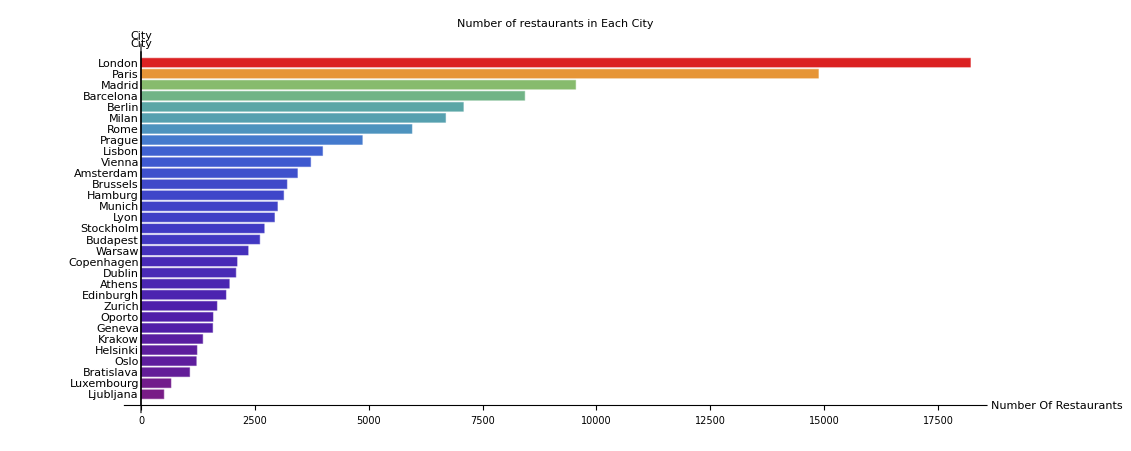

```mathematica
BarChart[Sort[Counts[finaldata[All,"City"]]],Axes->True,AxesLabel->{"City","Number Of Restaurants"},ChartLabels->Automatic,BarSpacing->Medium,BarOrigin->Left,ColorFunction->Function[{height},ColorData["Rainbow"][height]],PlotLabel->Style["Number of restaurants in Each City","Title",20],AspectRatio->Full]
```

The most restaurants are located in London followed by Paris. These two cities are the only ones with at least 10K singular restaurants. 
Whereas Ljubljana, Luxembourg have the least number of restaurants.
Place the cursor on the bar to see the count of Restaurants in that city.

## Average Number of Customer Reviews by City

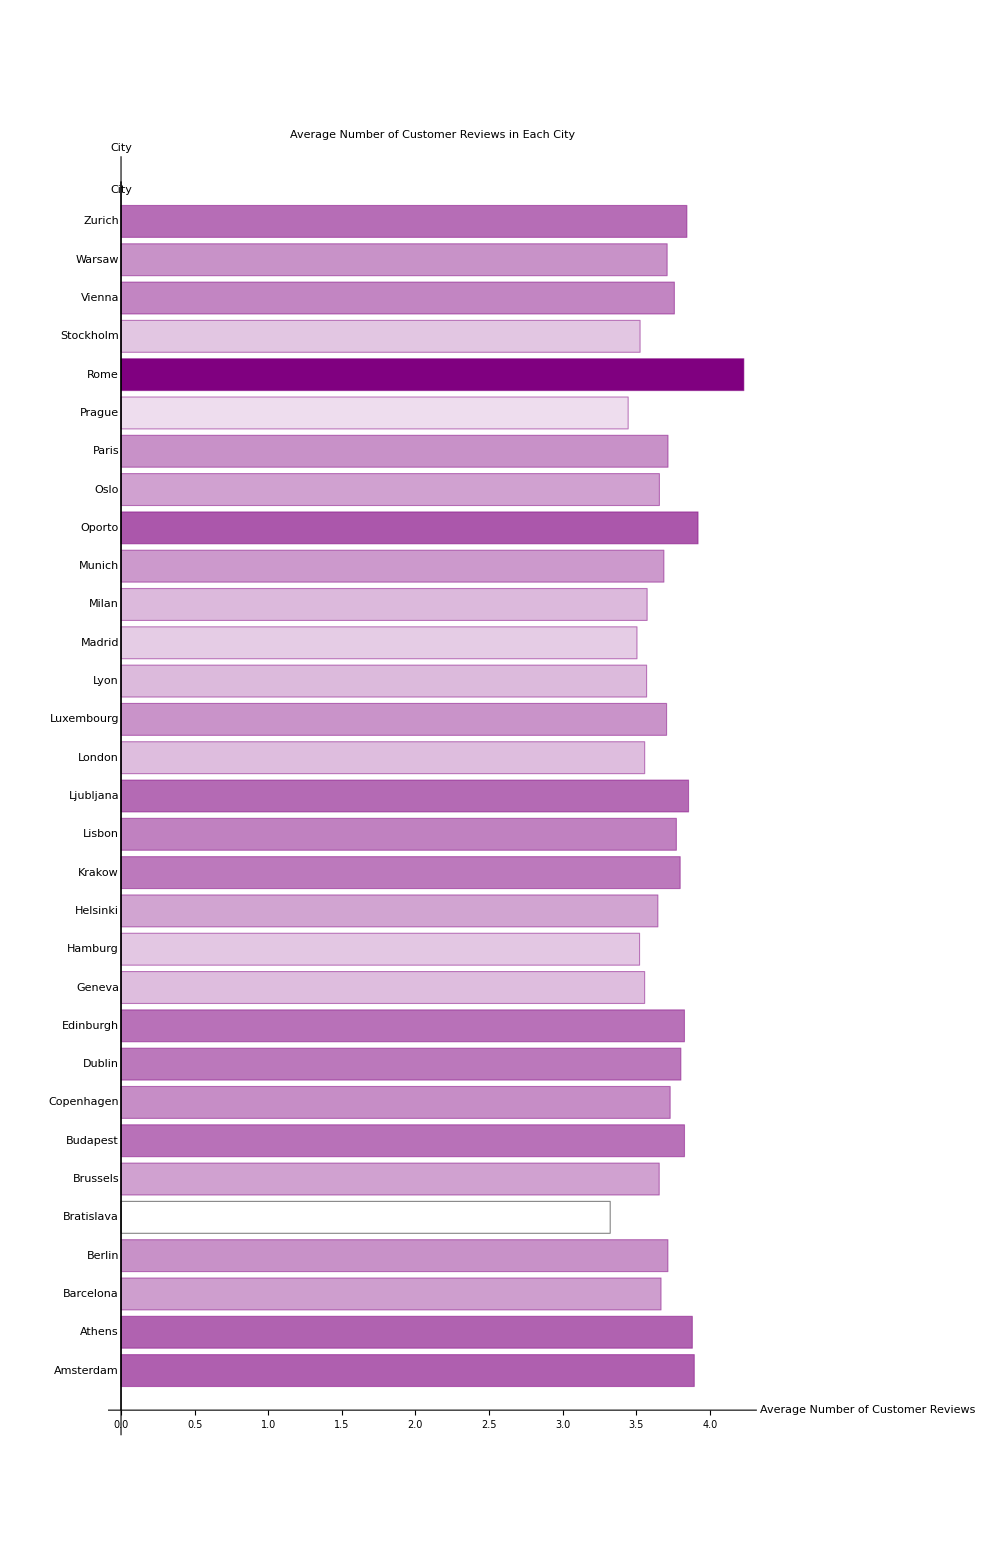

```mathematica
BarChart[finaldata[GroupBy["City"],<|""->Query[Mean,"Rating"]|>],Axes->True,AxesLabel->{"City","Average Number of Customer Reviews"},ChartLabels->Automatic,BarSpacing->Medium,BarOrigin->Left,ColorFunction->Function[{height},Opacity[height]],ChartStyle->Purple,PlotLabel->Style["Average Number of Customer Reviews in Each City","Title",20],AspectRatio->Full]
```

Even though London and Paris are the top 2 in number of restaurants, their average number of reviews are not very high compared to the others. It seems more people like to review the restaurants in Rome, Oporto, and Amsterdam more than others.

## Price Range of all Restaurants

```mathematica
groups=Counts[finaldata[All,"Price Range"]]
```

Dataset[<>]

$$-$$$ means Average Priced Restaurants
$$$$ means Expensive Priced Restaurants
$ means Cheap Priced Restaurants
0 means Unknown,the Price Range is not mentioned in the dataset.

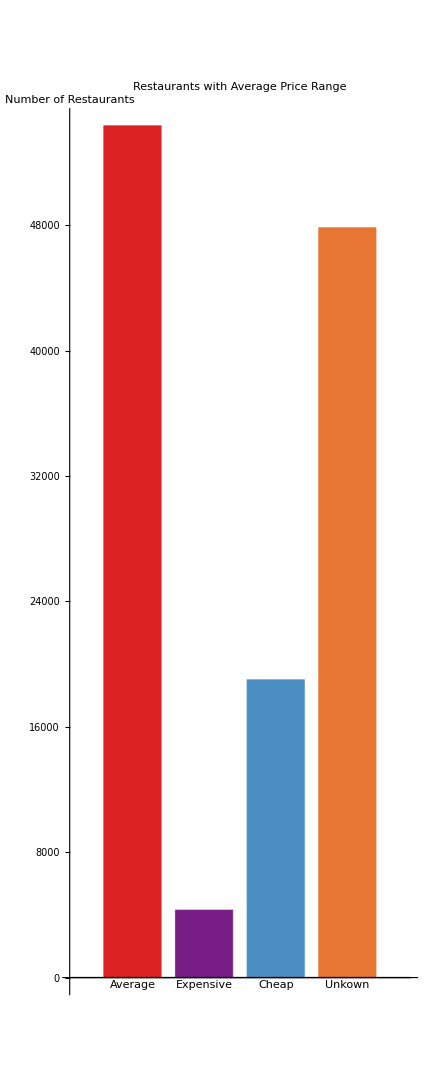

```mathematica
BarChart[groups,Axes->True,AxesLabel->{"","Number of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Restaurants with Average Price Range","Title",20],AspectRatio->Full]
```

By looking at the Bar Chart we can say that most of the restaurants are of Average Price Range followed by very few restaurants are Expensive,approximately 19k restaurants are priced cheaper compared to the other restaurants,relatively most restaurants price have not been mentioned in the dataset.

## Restaurants and Price Range per City

Here i am trying to explore which city most expensive restaurant,most cheap restaurants and average priced restaurants.
Please place the cursor on the bar to get the number of restaurants.

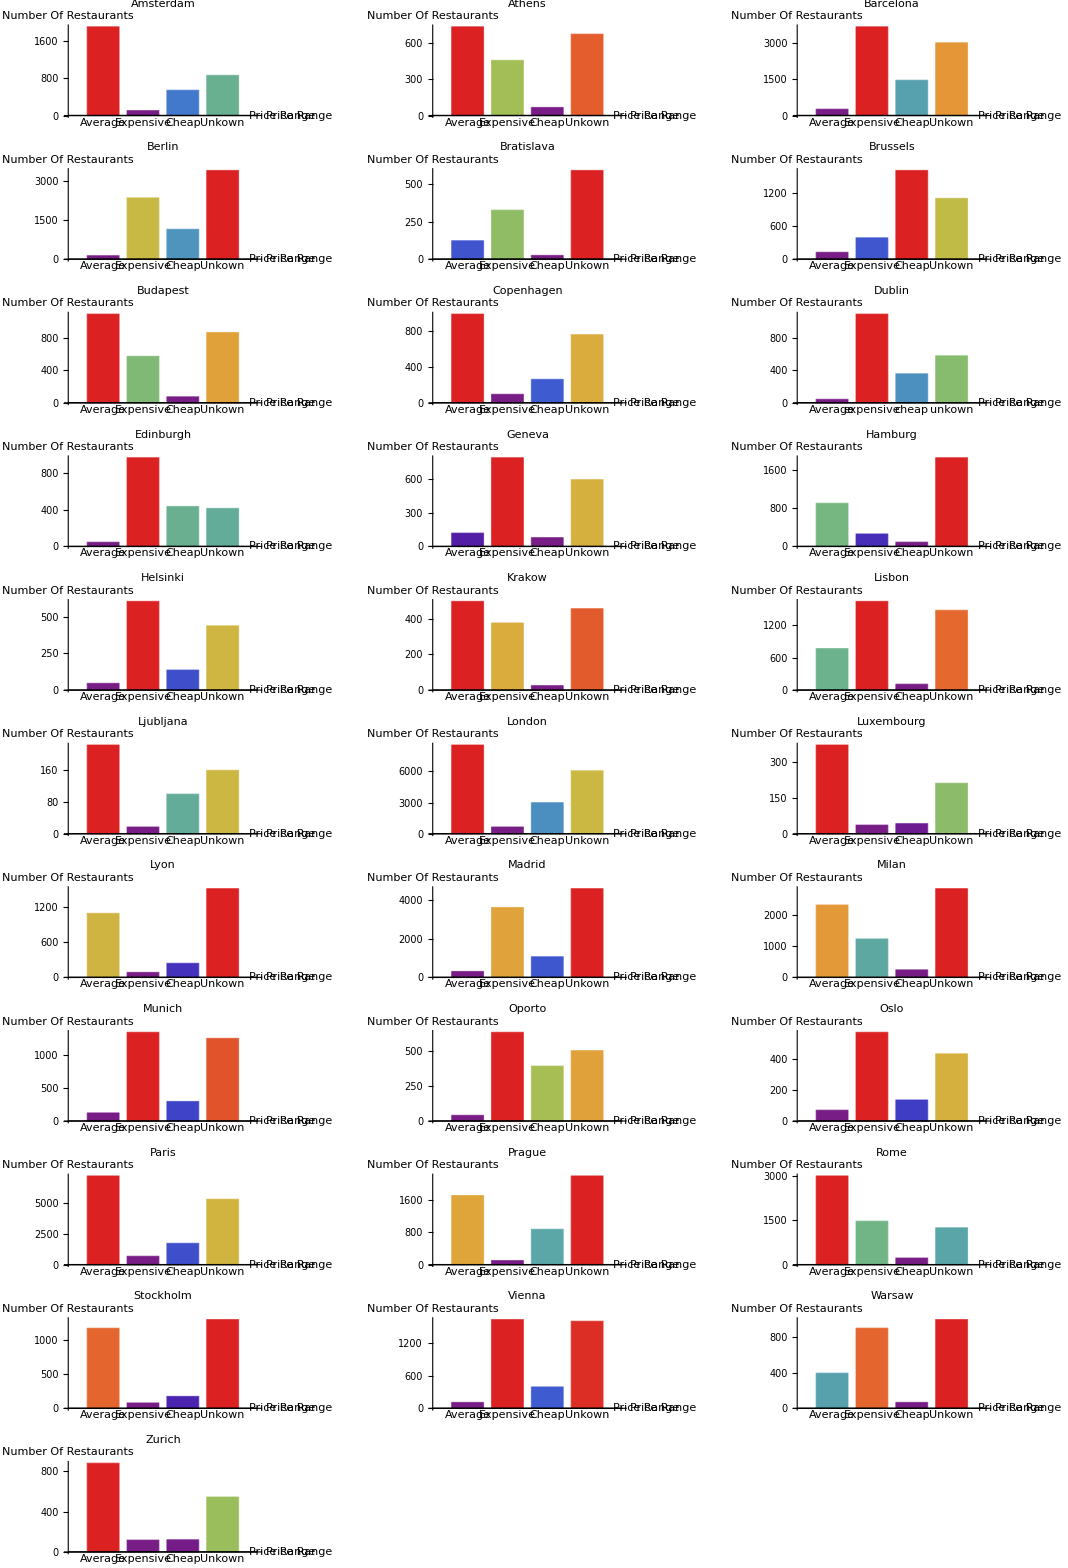

```mathematica
cs=finaldata[GroupBy["City"]];
groupsAms=Counts[cs["Amsterdam"][[All,"Price Range"]]];
b1=BarChart[groupsAms,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Amsterdam","Title",16],AspectRatio->Full];
groupsAth=Counts[cs["Athens"][[All,"Price Range"]]];
b2=BarChart[groupsAth,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Athens","Title",16],AspectRatio->Full];
groupsBarc=Counts[cs["Barcelona"][[All,"Price Range"]]];
b3=BarChart[groupsBarc,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Barcelona","Title",16],AspectRatio->Full];
groupsBer=Counts[cs["Berlin"][[All,"Price Range"]]];
b4=BarChart[groupsBer,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Berlin","Title",16],AspectRatio->Full];
groupsBrat=Counts[cs["Bratislava"][[All,"Price Range"]]];
b5=BarChart[groupsBrat,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Bratislava","Title",16],AspectRatio->Full];
groupsBrus=Counts[cs["Brussels"][[All,"Price Range"]]];
b6=BarChart[groupsBrus,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Brussels","Title",16],AspectRatio->Full];
groupsBuda=Counts[cs["Budapest"][[All,"Price Range"]]];
b7=BarChart[groupsBuda,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Budapest","Title",16],AspectRatio->Full];
groupsCope=Counts[cs["Copenhagen"][[All,"Price Range"]]];
b8=BarChart[groupsCope,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Copenhagen","Title",16],AspectRatio->Full];
groupsDub=Counts[cs["Dublin"][[All,"Price Range"]]];
b9=BarChart[groupsDub,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","expensive","cheap","unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Dublin","Title",16],AspectRatio->Full];
groupsEdin=Counts[cs["Edinburgh"][[All,"Price Range"]]];
b10=BarChart[groupsEdin,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Edinburgh","Title",16],AspectRatio->Full];
groupsGen=Counts[cs["Geneva"][[All,"Price Range"]]];
b11=BarChart[groupsGen,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Geneva","Title",16],AspectRatio->Full];
groupsHam=Counts[cs["Hamburg"][[All,"Price Range"]]];
b12=BarChart[groupsHam,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Hamburg","Title",16],AspectRatio->Full];
groupsHel=Counts[cs["Helsinki"][[All,"Price Range"]]];
b13=BarChart[groupsHel,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Helsinki","Title",16],AspectRatio->Full];
groupsKra=Counts[cs["Krakow"][[All,"Price Range"]]];
b14=BarChart[groupsKra,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Krakow","Title",16],AspectRatio->Full];
groupsLis=Counts[cs["Lisbon"][[All,"Price Range"]]];
b15=BarChart[groupsLis,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Lisbon","Title",16],AspectRatio->Full];
groupsLju=Counts[cs["Ljubljana"][[All,"Price Range"]]];
b16=BarChart[groupsLju,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Ljubljana","Title",16],AspectRatio->Full];
groupsLon=Counts[cs["London"][[All,"Price Range"]]];
b17=BarChart[groupsLon,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["London","Title",16],AspectRatio->Full];
groupsLux=Counts[cs["Luxembourg"][[All,"Price Range"]]];
b18=BarChart[groupsLux,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Luxembourg","Title",16],AspectRatio->Full];
groupsLyo=Counts[cs["Lyon"][[All,"Price Range"]]];
b19=BarChart[groupsLyo,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Lyon","Title",16],AspectRatio->Full];
groupsMad=Counts[cs["Madrid"][[All,"Price Range"]]];
b20=BarChart[groupsMad,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Madrid","Title",16],AspectRatio->Full];
groupsMil=Counts[cs["Milan"][[All,"Price Range"]]];
b21=BarChart[groupsMil,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Milan","Title",16],AspectRatio->Full];
groupsMun=Counts[cs["Munich"][[All,"Price Range"]]];
b22=BarChart[groupsMun,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Munich","Title",16],AspectRatio->Full];
groupsOp=Counts[cs["Oporto"][[All,"Price Range"]]];
b23=BarChart[groupsOp,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Oporto","Title",16],AspectRatio->Full];
groupsOs=Counts[cs["Oslo"][[All,"Price Range"]]];
b24=BarChart[groupsOs,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Oslo","Title",16],AspectRatio->Full];
groupsPar=Counts[cs["Paris"][[All,"Price Range"]]];
b25=BarChart[groupsPar,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Paris","Title",16],AspectRatio->Full];
groupsPra=Counts[cs["Prague"][[All,"Price Range"]]];
b26=BarChart[groupsPra,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Prague","Title",16],AspectRatio->Full];
groupsRom=Counts[cs["Rome"][[All,"Price Range"]]];
b27=BarChart[groupsRom,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Rome","Title",16],AspectRatio->Full];
groupsSto=Counts[cs["Stockholm"][[All,"Price Range"]]];
b28=BarChart[groupsSto,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Stockholm","Title",16],AspectRatio->Full];
groupsVie=Counts[cs["Vienna"][[All,"Price Range"]]];
b29=BarChart[groupsVie,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Vienna","Title",16],AspectRatio->Full];
groupsWar=Counts[cs["Warsaw"][[All,"Price Range"]]];
b30=BarChart[groupsWar,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Warsaw","Title",16],AspectRatio->Full];
groupsZur=Counts[cs["Zurich"][[All,"Price Range"]]];
b31=BarChart[groupsZur,Axes->True,AxesLabel->{"Price Range","Number Of Restaurants"},ChartLabels->{"Average","Expensive","Cheap","Unkown"},BarSpacing->Medium,ColorFunction->"Rainbow",PlotLabel->Style["Zurich","Title",16],AspectRatio->Full];
GraphicsGrid[{{b1,b2,b3},{b4,b5,b6},{b7,b8,b9},{b10,b11,b12},{b13,b14,b15},{b16,b17,b18},{b19,b20,b21},{b22,b23,b24},{b25,b26,b27},{b28,b29,b30},{b31}}]
```

We can see here that all cities have the most number of restaurants in the Average price range. The only city with much more expensive restaurants than cheap ones is Brussels. Luxembourg and Zurich have almost an equal number of cheap and expensive restaurants in their cities. The remaining all have more cheaper restaurants than expensive.

## Cuisine Style

Here I am going to explore which type of Cuisine most of the Restaurants offer .

```mathematica
fr=Counts[StringCount[Finaldata[[All,4]],"French"]];
vg = Counts[StringCount[Finaldata[[All,4]],"Vegetarian Friendly"]];
in =Counts[StringCount[Finaldata[[All,4]],"International"]];
it = Counts[StringCount[Finaldata[[All,4]],"Italian"]];
gu = Counts[StringCount[Finaldata[[All,4]],"Gluten Free Options"]];
eu = Counts[StringCount[Finaldata[[All,4]],"European"]];
cf = Counts[StringCount[Finaldata[[All,4]],"Cafe"]];
co =Counts[StringCount[Finaldata[[All,4]],"Contemporary"]];
ind = Counts[StringCount[Finaldata[[All,4]],"Indian"]];
ba =Counts[StringCount[Finaldata[[All,4]],"Bar"]];
sp = Counts[StringCount[Finaldata[[All,4]],"Spanish"]];
md=  Counts[StringCount[Finaldata[[All,4]],"Mediterranean"]] ;
vo = Counts[StringCount[Finaldata[[All,4]],"Vegan Options"]];
PieChart[{fr[1],vg[1],in[1],it[1],gu[1],eu[1],cf[1],co[1],ind[1],ba[1],sp[1],md[1],vo[1]},ChartLabels->Callout[{"French","Vegetreian Friendly","International","Italian","Gluten Free","European","Cafe","Contemporary","Indian","Bar","Spanish","Mediterranean","Vegan Options"}]]
```

-Graphics-

By analysing the pie chart we can say that most of the restaurants offer Vegetarian Friendly and European,whereas the Indian and Contemporary are the least.

## The Top 3 Budget Friendly vs Expensive Restaurants

For these visuals, I’ll use the ranking and the Price Ranges Cheap and Expensive for the Restaurants in selected cities: Amsterdam,Dublin and London.
This can be also be done to any country.

### Budget Friendly Restaurants

### Amsterdam:

```mathematica
amster=cs[1][GroupBy["Price Range"]][3][[Range[1,3],{"Name","Ranking"}]]
```

Dataset[<>]

The above restaurants are the best 3 and cheap restaurants in Amsterdam.

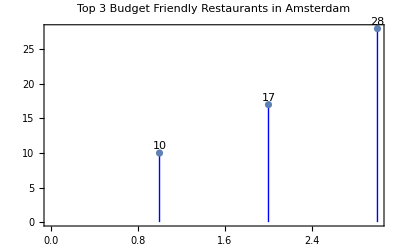

```mathematica
ListPlot[amster[[All,"Ranking"]],Filling->Bottom,FillingStyle->{Blue},LabelingFunction->Above,PlotLabel->"Top 3 Budget Friendly Restaurants in Amsterdam",Frame->True]
```

### Dublin:

```mathematica
dub=cs[9][GroupBy["Price Range"]][3][[Range[1,3],{"Name","Ranking"}]]
```

Dataset[<>]

The above restaurants are the best 3 and cheap restaurants in Dublin.

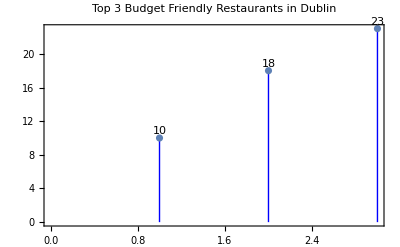

```mathematica
ListPlot[dub[[All,"Ranking"]],Filling->Bottom,FillingStyle->{Blue},LabelingFunction->Above,PlotLabel->"Top 3 Budget Friendly Restaurants in Dublin",Frame->True]
```

### London:

```mathematica
cs[17]
```

```mathematica
lon=cs[17][GroupBy["Price Range"]][3][[Range[1,3],{"Name","Ranking"}]]
```

Dataset[<>]

The above restaurants are the best 3 and cheap restaurants in London.

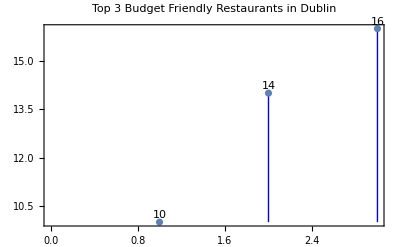

```mathematica
ListPlot[lon[[All,"Ranking"]],Filling->Bottom,FillingStyle->{Blue},LabelingFunction->Above,PlotLabel->"Top 3 Budget Friendly Restaurants in Dublin",Frame->True]
```

### Expensive Restaurants

#### Amsterdam:

```mathematica
amsterexp = cs[1][GroupBy["Price Range"]][2][[Range[1,3],{"Name","Ranking"}]]
```

Dataset[<>]

The above restaurants are the most  expensive restaurants in Amsterdam.

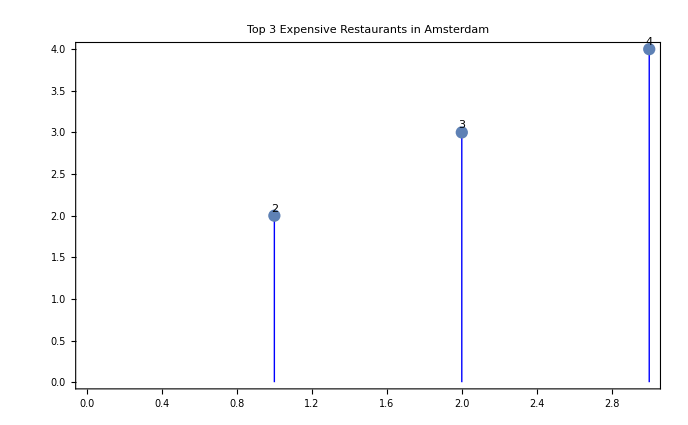

```mathematica
ListPlot[amsterexp[[All,"Ranking"]],Filling->Bottom,FillingStyle->{Blue},LabelingFunction->Above,PlotLabel->"Top 3 Expensive Restaurants in Amsterdam",Frame->True]
```

#### Dublin:

```mathematica
dubexp = cs[9][GroupBy["Price Range"]][2][[Range[1,3],{"Name","Ranking"}]]
```

Dataset[<>]

The above restaurants are the most  expensive restaurants in Dublin.

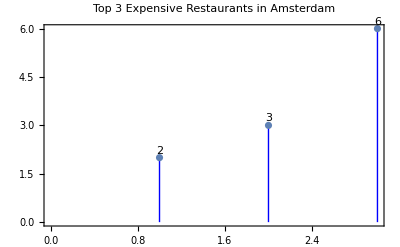

```mathematica
ListPlot[dubexp[[All,"Ranking"]],Filling->Bottom,FillingStyle->{Blue},LabelingFunction->Above,PlotLabel->"Top 3 Expensive Restaurants in Amsterdam",Frame->True]
```

#### London:

```mathematica
lonexp = cs[17][GroupBy["Price Range"]][2][[Range[1,3],{"Name","Ranking"}]]
```

Dataset[<>]

The above restaurants are the most  expensive restaurants in London.

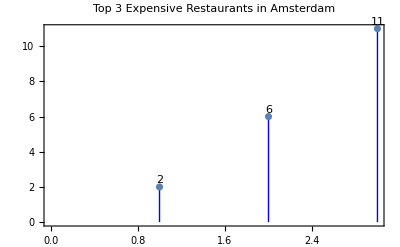

```mathematica
ListPlot[lonexp[[All,"Ranking"]],Filling->Bottom,FillingStyle->{Blue},LabelingFunction->Above,PlotLabel->"Top 3 Expensive Restaurants in Amsterdam",Frame->True]
```

## Cuisine Favorites Based on your favourite cuisine,you can pick the top Restaurants based on the city you visit.

```mathematica
gcs =finaldata[GroupBy["Cuisine Style"]];
```

#### Indian:

```mathematica
gcs[997]
```

Dataset[<>]

#### European

```mathematica
gcs[839]
```

Dataset[<>]

#### European

```mathematica
gcs[786]
```

Dataset[<>]

#### Vegetarian Friendly

```mathematica
gcs[646]
```

Dataset[<>]

#### Cafes

```mathematica
gcs[300]
```

Dataset[<>]

#### Bars

```mathematica
gcs[111][[Range[1,25],{"Name","Ranking","City"}]]
```

Dataset[<>]

## Word Frequency

Due to my limited resource ,I have loaded the data only with the review column.It takes longer time for the computation.
I am going to the perform some operation on review column.
I am going to find out the frequency of the words like food,great,very.etc.

```mathematica
data = Import["C:/Users/NIKHIL BADRI PRASAD/Documents/Wolfram Mathematica/Test1.csv"];
```

```mathematica
Counts[WordFrequency[data[[All,9]],"food"]];
Counts[WordFrequency[data[[All,9]],"great"]];
{{Counts[WordFrequency[data[[All,9]],"very"]];}, {Counts[WordFrequency[data[[All,9]],"best"]];}, {Counts[WordFrequency[data[[All,9]],"Amazing"]];}}
Counts[WordFrequency[data[[All,9]],"Awesome"]];
Counts[WordFrequency[data[[All,9]],"recommend"]];
Counts[WordFrequency[data[[All,9]],"meal"]];
Counts[WordFrequency[data[[All,9]],"value"]];
Counts[WordFrequency[data[[All,9]],"staff"]];
```

## Word Cloud

This is the  visualised view of the most words used in the review.

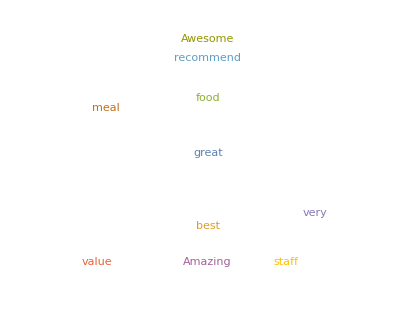

```mathematica
WordCloud[<|"food"->4,"great"->9,"very"->3,"best"->4,"Amazing"->1,"Awesome"->1,"recommend"->2,"meal"->2,"value"->3,"staff"->2|>]
```

## Conclusion

I think with the analysis above, there are many answers to the question “Where should you eat in Europe?”. There are many Restaurants in these European cities and a variety of cuisines and price ranges to choose from. So you have a lot of options depending on where you are and what you feel like eating. More visuals can be done with this dataset but I think for now I’ve covered the ones that seem the most interesting and useful.